```mathematica
EdgeList[CycleGraph[5]]//Sort
```

{1<->2,1<->5,2<->3,3<->4,4<->5}

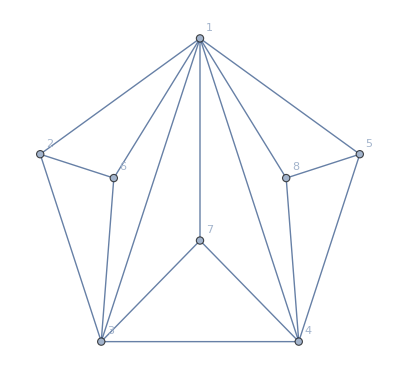

```mathematica
g=Graph[{1<->2,1<->5,2<->3,3<->4,4<->5,1<->3,1<->4,6<->1,6<->2,6<->3,7<->1,7<->4,7<->3,8<->1,8<->4,8<->5}, GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
```

```mathematica
Solve[ToLogical[g]&&x1==1&&x2==2&&x3==3&&x4==4&&x5==3]
```

{{x1→1,x2→2,x3→3,x4→4,x5→3,x6→4,x7→2,x8→2}}

```mathematica
GraphSolutions2[g,x1==1&&x2==4&&x3==3&&x4==4&&x5==3,GraphLayout->"TutteEmbedding"]
```

GraphSolutions2[-Graphics-,x1==1&&x2==4&&x3==3&&x4==4&&x5==3,GraphLayout→TutteEmbedding]

```mathematica
GraphSolutions2[g]
```

{{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→2,x8→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→2,x8→4},{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→4,x8→4},{x1→1,x2→2,x3→3,x4→4,x5→3,x6→4,x7→2,x8→2},{x1→1,x2→2,x3→4,x4→2,x5→3,x6→3,x7→3,x8→4},{x1→1,x2→2,x3→3,x4→2,x5→4,x6→4,x7→4,x8→3},{x1→1,x2→2,x3→4,x4→2,x5→4,x6→3,x7→3,x8→3},{x1→1,x2→2,x3→4,x4→3,x5→4,x6→3,x7→2,x8→2},{x1→1,x2→3,x3→2,x4→3,x5→2,x6→4,x7→4,x8→4},{x1→1,x2→3,x3→2,x4→4,x5→2,x6→4,x7→3,x8→3},{x1→1,x2→3,x3→4,x4→3,x5→2,x6→2,x7→2,x8→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→3,x8→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→3,x8→4},{x1→1,x2→3,x3→2,x4→3,x5→4,x6→4,x7→4,x8→2},{x1→1,x2→3,x3→4,x4→2,x5→4,x6→2,x7→3,x8→3},{x1→1,x2→3,x3→4,x4→3,x5→4,x6→2,x7→2,x8→2},{x1→1,x2→4,x3→2,x4→3,x5→2,x6→3,x7→4,x8→4},{x1→1,x2→4,x3→2,x4→4,x5→2,x6→3,x7→3,x8→3},{x1→1,x2→4,x3→3,x4→4,x5→2,x6→2,x7→2,x8→3},{x1→1,x2→4,x3→2,x4→4,x5→3,x6→3,x7→3,x8→2},{x1→1,x2→4,x3→3,x4→2,x5→3,x6→2,x7→4,x8→4},{x1→1,x2→4,x3→3,x4→4,x5→3,x6→2,x7→2,x8→2},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→4,x8→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→4,x8→3},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→1,x8→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→1,x8→4},{x1→2,x2→1,x3→3,x4→1,x5→3,x6→4,x7→4,x8→4},{x1→2,x2→1,x3→3,x4→4,x5→3,x6→4,x7→1,x8→1},{x1→2,x2→1,x3→4,x4→1,x5→3,x6→3,x7→3,x8→4},{x1→2,x2→1,x3→3,x4→1,x5→4,x6→4,x7→4,x8→3},{x1→2,x2→1,x3→4,x4→1,x5→4,x6→3,x7→3,x8→3},{x1→2,x2→1,x3→4,x4→3,x5→4,x6→3,x7→1,x8→1},{x1→2,x2→3,x3→1,x4→3,x5→1,x6→4,x7→4,x8→4},{x1→2,x2→3,x3→1,x4→4,x5→1,x6→4,x7→3,x8→3},{x1→2,x2→3,x3→4,x4→3,x5→1,x6→1,x7→1,x8→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→3,x8→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→3,x8→4},{x1→2,x2→3,x3→1,x4→3,x5→4,x6→4,x7→4,x8→1},{x1→2,x2→3,x3→4,x4→1,x5→4,x6→1,x7→3,x8→3},{x1→2,x2→3,x3→4,x4→3,x5→4,x6→1,x7→1,x8→1},{x1→2,x2→4,x3→1,x4→3,x5→1,x6→3,x7→4,x8→4},{x1→2,x2→4,x3→1,x4→4,x5→1,x6→3,x7→3,x8→3},{x1→2,x2→4,x3→3,x4→4,x5→1,x6→1,x7→1,x8→3},{x1→2,x2→4,x3→1,x4→4,x5→3,x6→3,x7→3,x8→1},{x1→2,x2→4,x3→3,x4→1,x5→3,x6→1,x7→4,x8→4},{x1→2,x2→4,x3→3,x4→4,x5→3,x6→1,x7→1,x8→1},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→4,x8→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→4,x8→3},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→1,x8→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→1,x8→4},{x1→3,x2→1,x3→2,x4→1,x5→2,x6→4,x7→4,x8→4},{x1→3,x2→1,x3→2,x4→4,x5→2,x6→4,x7→1,x8→1},{x1→3,x2→1,x3→4,x4→1,x5→2,x6→2,x7→2,x8→4},{x1→3,x2→1,x3→2,x4→1,x5→4,x6→4,x7→4,x8→2},{x1→3,x2→1,x3→4,x4→1,x5→4,x6→2,x7→2,x8→2},{x1→3,x2→1,x3→4,x4→2,x5→4,x6→2,x7→1,x8→1},{x1→3,x2→2,x3→1,x4→2,x5→1,x6→4,x7→4,x8→4},{x1→3,x2→2,x3→1,x4→4,x5→1,x6→4,x7→2,x8→2},{x1→3,x2→2,x3→4,x4→2,x5→1,x6→1,x7→1,x8→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→2,x8→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→2,x8→4},{x1→3,x2→2,x3→1,x4→2,x5→4,x6→4,x7→4,x8→1},{x1→3,x2→2,x3→4,x4→1,x5→4,x6→1,x7→2,x8→2},{x1→3,x2→2,x3→4,x4→2,x5→4,x6→1,x7→1,x8→1},{x1→3,x2→4,x3→1,x4→2,x5→1,x6→2,x7→4,x8→4},{x1→3,x2→4,x3→1,x4→4,x5→1,x6→2,x7→2,x8→2},{x1→3,x2→4,x3→2,x4→4,x5→1,x6→1,x7→1,x8→2},{x1→3,x2→4,x3→1,x4→4,x5→2,x6→2,x7→2,x8→1},{x1→3,x2→4,x3→2,x4→1,x5→2,x6→1,x7→4,x8→4},{x1→3,x2→4,x3→2,x4→4,x5→2,x6→1,x7→1,x8→1},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→4,x8→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→4,x8→2},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→1,x8→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→1,x8→3},{x1→4,x2→1,x3→2,x4→1,x5→2,x6→3,x7→3,x8→3},{x1→4,x2→1,x3→2,x4→3,x5→2,x6→3,x7→1,x8→1},{x1→4,x2→1,x3→3,x4→1,x5→2,x6→2,x7→2,x8→3},{x1→4,x2→1,x3→2,x4→1,x5→3,x6→3,x7→3,x8→2},{x1→4,x2→1,x3→3,x4→1,x5→3,x6→2,x7→2,x8→2},{x1→4,x2→1,x3→3,x4→2,x5→3,x6→2,x7→1,x8→1},{x1→4,x2→2,x3→1,x4→2,x5→1,x6→3,x7→3,x8→3},{x1→4,x2→2,x3→1,x4→3,x5→1,x6→3,x7→2,x8→2},{x1→4,x2→2,x3→3,x4→2,x5→1,x6→1,x7→1,x8→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→2,x8→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→2,x8→3},{x1→4,x2→2,x3→1,x4→2,x5→3,x6→3,x7→3,x8→1},{x1→4,x2→2,x3→3,x4→1,x5→3,x6→1,x7→2,x8→2},{x1→4,x2→2,x3→3,x4→2,x5→3,x6→1,x7→1,x8→1},{x1→4,x2→3,x3→1,x4→2,x5→1,x6→2,x7→3,x8→3},{x1→4,x2→3,x3→1,x4→3,x5→1,x6→2,x7→2,x8→2},{x1→4,x2→3,x3→2,x4→3,x5→1,x6→1,x7→1,x8→2},{x1→4,x2→3,x3→1,x4→3,x5→2,x6→2,x7→2,x8→1},{x1→4,x2→3,x3→2,x4→1,x5→2,x6→1,x7→3,x8→3},{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→1,x8→1},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→3,x8→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→3,x8→2}}

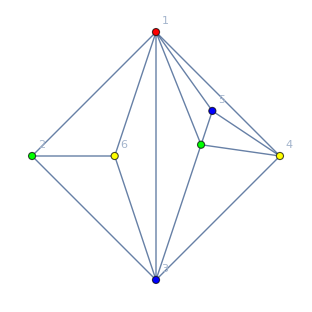

```mathematica
PaintGraph3[VertexContract[g,{7,8}],x1==1&&x2==2&&x3==3&&x4==4&&x5==3,GraphLayout->"TutteEmbedding"]
```

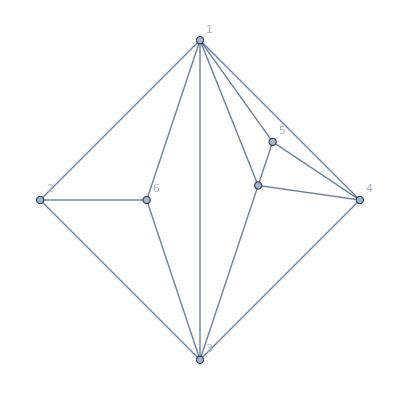

```mathematica
VertexContract[g,{7,8}]
```

```mathematica
VertexCount[Graph[plantri[[1]]]]
```

12

```mathematica
formula1=FindFullFormula[Graph[plantri[[1]]]];Put[formula1,"d:\\Saved\\formula1.m"]
```

```mathematica
With[
{c=ChromaticPolynomial[Graph[plantri[[8]]]]},
Table[c[x],{x,0,17}]
]
```

{0,0,0,0,528,4356360,1319826240,95827360440,2961196832160,51703691821488,599959907910720,5122222999969680,34440402315916080,191278993262505720,908534068501707648,3788033204198323080,14144907500272960320,48056250613322941920}

```mathematica
Length[formula1]
```

26793

```mathematica
With[
{c=ChromaticPolynomial[Graph[plantri[[1]]]]},
Table[c[x]/x!,{x,0,12}]
]
```

{0,0,0,0,10,670,5573,45743/3,245669/12,198595/12,655057/72,9277343/2520,23348933/20160}

```mathematica
Tally[Map[StringCount[SymbolName[#],"x"]+1&,formula1]]
```

{{12,1},{11,36},{10,470},{9,2800},{8,7900},{7,10008},{6,4908},{5,660},{4,10}}

```mathematica
Select[formula1,StringCount[SymbolName[#],"x"]+1==4&]
```

{v19bx25cx37ax468,v19bx24cx357x68a,v18ax29bx357x46c,v18bx259x37ax46c,v18bx24cx36ax579,v18ax24bx36cx579,v17ax29bx35cx468,v17ax259x36cx48b,v179x25cx36ax48b,v179x24bx35cx68a}

```mathematica
IsRefinement2[small_,big_]:=Block[{sets,result=False,merged, equal,small2,big2},
If[Length[small]+1==Length[big],
equal=Select[big,MemberQ[small,#]&];
If[Length[equal]==Length[small]-1,
small2=Select[small,!MemberQ[equal,#]&];
big2=Select[big,!MemberQ[equal,#]&];
small2=Sort[Flatten[small2]];
big2=Sort[Flatten[big2]];
If[small2==big2,result=True]
];
];
result
]
```

```mathematica
IsRefinement2[SymbolToSets[v1x2x34x5],SymbolToSets[v1x2x3x4x5]]
```

{{1},{2},{3,4},{5}}   {{1},{2},{3},{4},{5}}

{{1},{2},{5}}

True

```mathematica
Select[ListofVars[formula1],IsRefinement2[SymbolToSets[v19bx25cx37ax468],SymbolToSets[#]]&]
```

{v19bx25cx37ax46x8,v19bx25cx37ax48x6,v19bx25cx37ax4x68,v19bx25cx37x468xa,v19bx25cx3ax468x7,v19bx25cx3x468x7a,v19bx25x37ax468xc,v19bx2cx37ax468x5,v19bx2x37ax468x5c,v19x25cx37ax468xb,v1bx25cx37ax468x9,v1x25cx37ax468x9b}

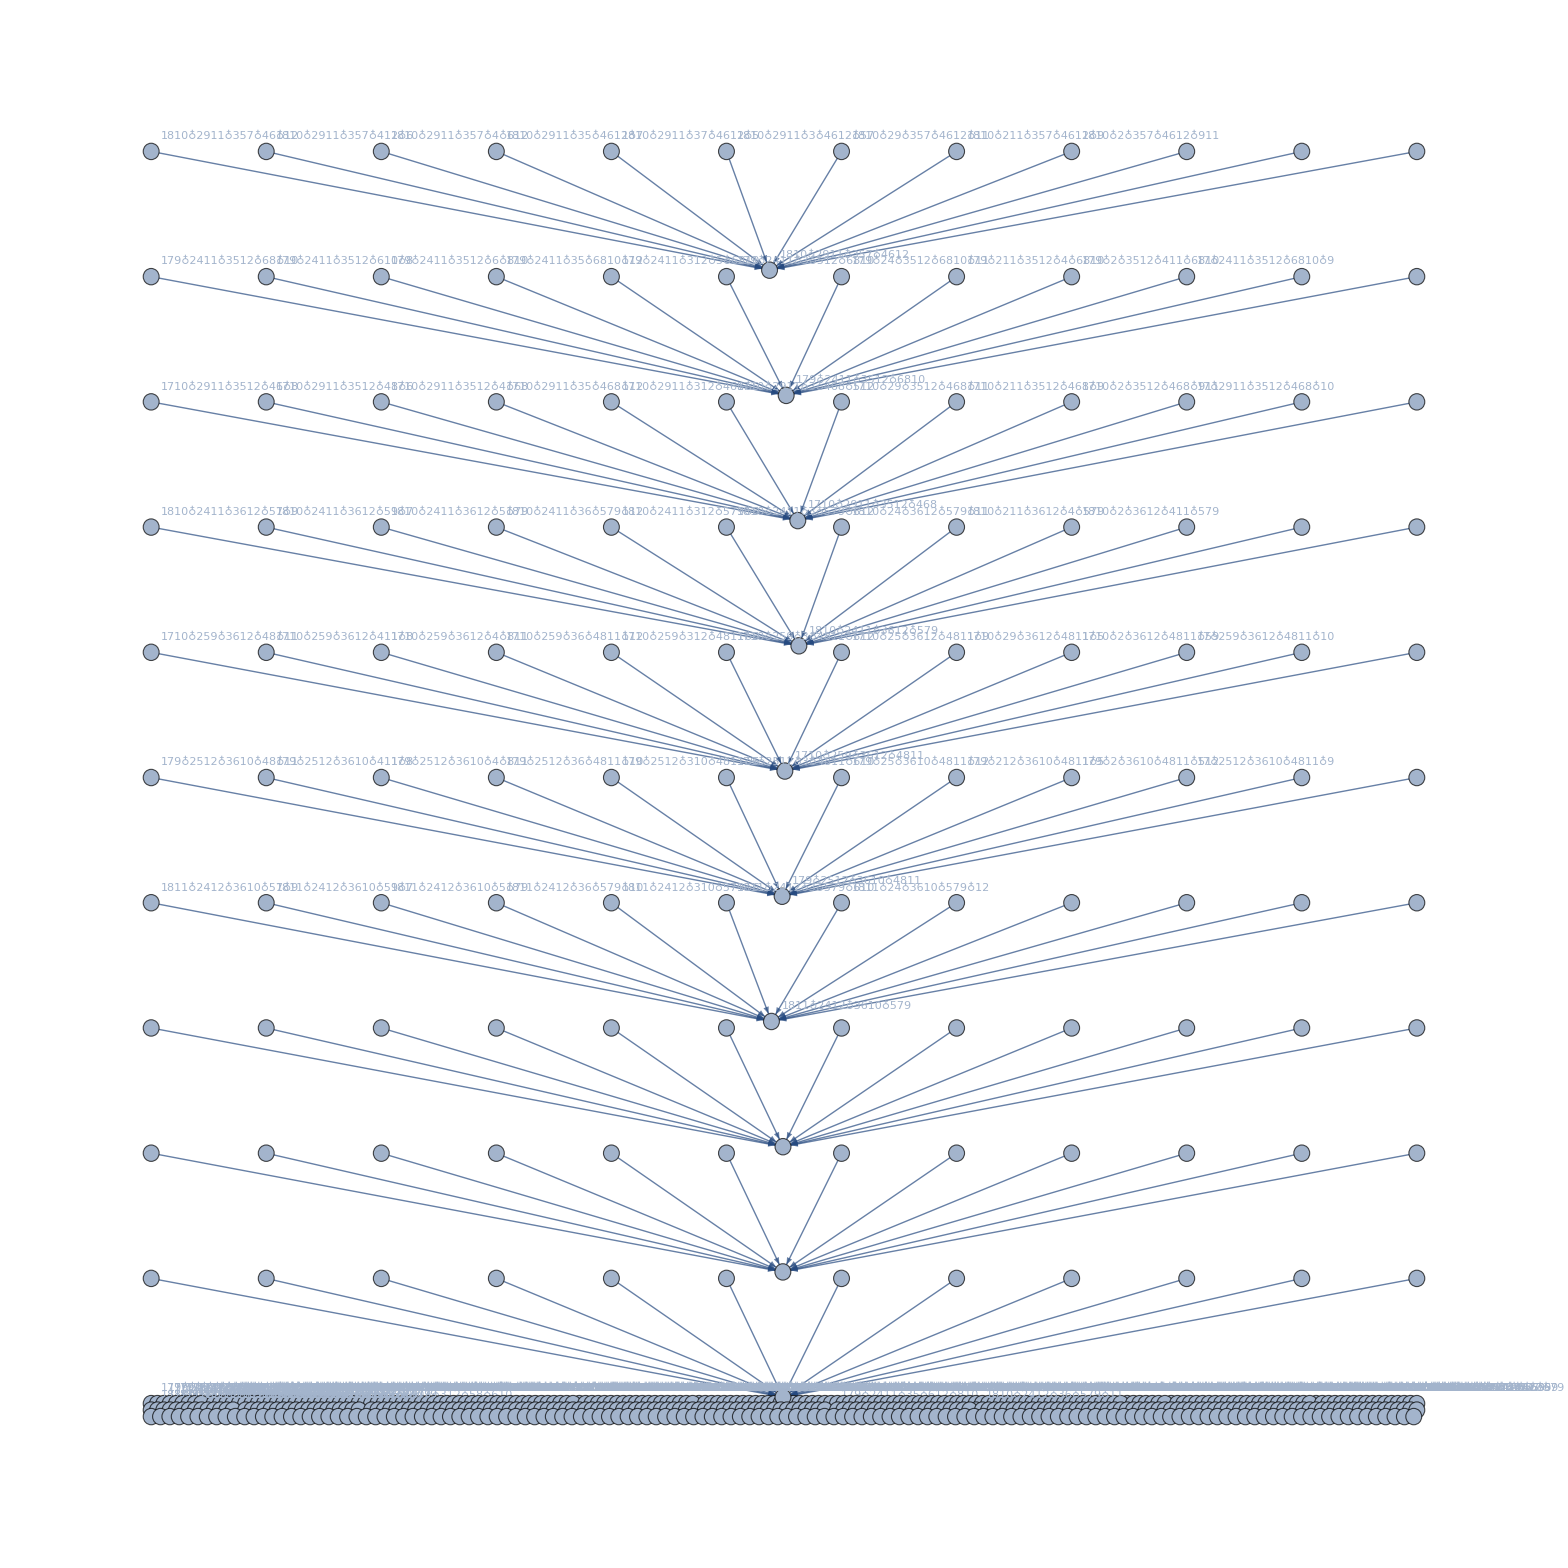

```mathematica
FormulaGraph[Select[formula1,StringCount[SymbolName[#],"x"]+1<6&]]
```

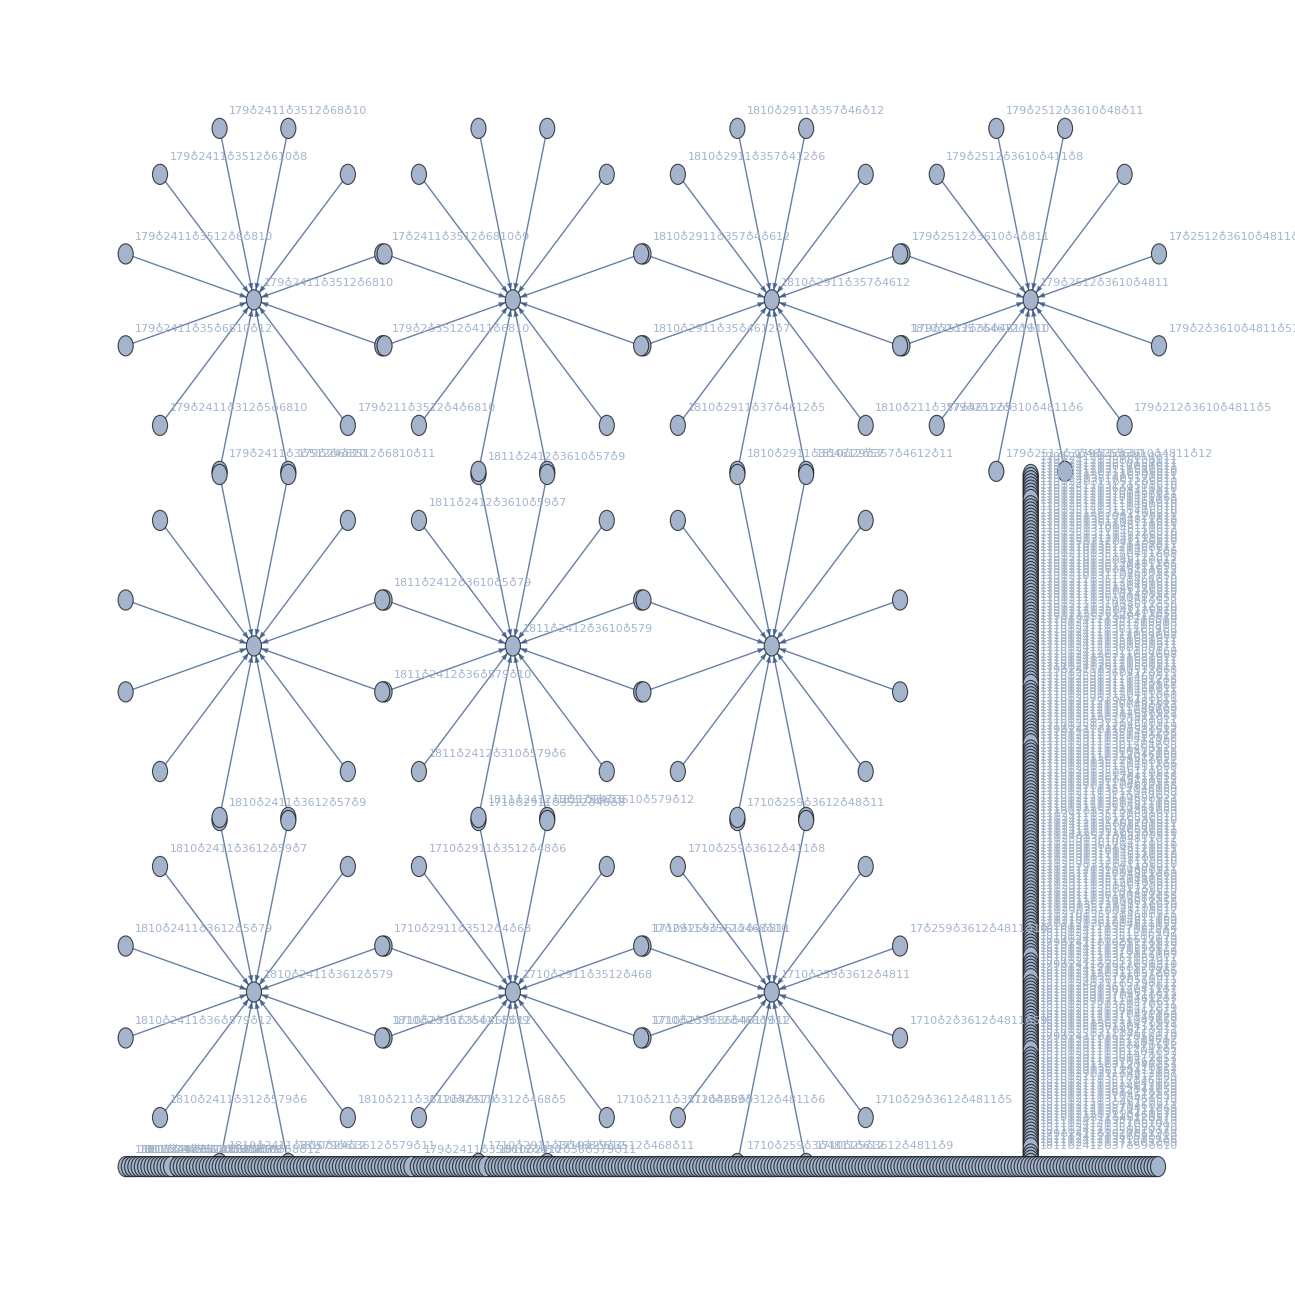

```mathematica
Graph[%,GraphLayout->"RadialDrawing"]
```

```mathematica
Map[SymbolToLabel2[#]&,Select[formula1,StringCount[SymbolName[#],"x"]+1<6&]]//Sort//TableForm
```

17♁24b♁35c♁68a
17♁259♁36a♁48b
17♁259♁36c♁48b
17♁25c♁36a♁48b
17♁29b♁35c♁468
17♁29b♁35c♁68a
179♁24♁35c♁68a
179♁24b♁35♁68a
179♁24b♁35c♁68
179♁24b♁35c♁68a
179♁24b♁35c♁6a
179♁24b♁35c♁8a
179♁24b♁36a♁58
179♁24b♁36a♁5c
179♁24b♁36c♁58
179♁24b♁36c♁8a
179♁24b♁3c♁68a
179♁24b♁5c♁68a
179♁24c♁35♁68a
179♁24c♁36a♁58
179♁24c♁36a♁8b
179♁24c♁3b♁68a
179♁25♁36a♁48b
179♁25♁36c♁48b
179♁25c♁36♁48b
179♁25c♁36a♁48
179♁25c♁36a♁48b
179♁25c♁36a♁4b
179♁25c♁36a♁8b
179♁25c♁3a♁468
179♁25c♁3a♁48b
179♁25c♁3b♁468
179♁25c♁3b♁68a
179♁25c♁48b♁6a
179♁25c♁4b♁68a
179♁2a♁35c♁468
179♁2a♁35c♁48b
179♁2a♁36c♁48b
179♁2b♁35c♁468
179♁2b♁35c♁68a
179♁2c♁36a♁48b
179♁35c♁48b♁6a
179♁35c♁4b♁68a
179♁36a♁48b♁5c
17a♁24b♁35c♁68
17a♁24b♁35c♁69
17a♁24b♁36c♁58
17a♁24b♁36c♁59
17a♁25♁36c♁48b
17a♁259♁36♁48b
17a♁259♁36c♁48
17a♁259♁36c♁48b
17a♁259♁36c♁4b
17a♁259♁36c♁8b
17a♁259♁3b♁468
17a♁259♁3b♁46c
17a♁259♁3c♁468
17a♁259♁3c♁48b
17a♁259♁46c♁8b
17a♁259♁48b♁6c
17a♁25c♁36♁48b
17a♁25c♁3b♁468
17a♁25c♁468♁9b
17a♁25c♁48b♁69
17a♁29♁35c♁468
17a♁29♁35c♁48b
17a♁29♁36c♁48b
17a♁29b♁35♁468
17a♁29b♁35♁46c
17a♁29b♁35c♁46
17a♁29b♁35c♁468
17a♁29b♁35c♁48
17a♁29b♁35c♁68
17a♁29b♁36c♁48
17a♁29b♁36c♁58
17a♁29b♁3c♁468
17a♁29b♁468♁5c
17a♁29b♁46c♁58
17a♁2b♁35c♁468
17a♁35c♁468♁9b
17a♁35c♁48b♁69
17a♁36c♁48b♁59
18♁24b♁36a♁579
18♁24b♁36c♁579
18♁24c♁36a♁579
18♁259♁37a♁46c
18♁29b♁357♁46c
18♁29b♁37a♁46c
18a♁24♁36c♁579
18a♁24b♁357♁69
18a♁24b♁357♁6c
18a♁24b♁35c♁69
18a♁24b♁35c♁79
18a♁24b♁36♁579
18a♁24b♁36c♁57
18a♁24b♁36c♁579
18a♁24b♁36c♁59
18a♁24b♁36c♁79
18a♁24b♁3c♁579
18a♁24b♁579♁6c
18a♁24c♁357♁69
18a♁24c♁357♁9b
18a♁24c♁36♁579
18a♁24c♁3b♁579
18a♁259♁36c♁47
18a♁259♁36c♁4b
18a♁259♁37♁46c
18a♁259♁3b♁46c
18a♁29♁357♁46c
18a♁29b♁35♁46c
18a♁29b♁357♁46
18a♁29b♁357♁46c
18a♁29b♁357♁4c
18a♁29b♁357♁6c
18a♁29b♁35c♁46
18a♁29b♁35c♁47
18a♁29b♁36c♁47
18a♁29b♁36c♁57
18a♁29b♁37♁46c
18a♁29b♁46c♁57
18a♁2b♁357♁46c
18a♁2b♁36c♁579
18a♁2b♁46c♁579
18a♁357♁46c♁9b
18a♁36c♁4b♁579
18a♁3b♁46c♁579
18b♁24♁36a♁579
18b♁24♁36c♁579
18b♁24c♁357♁69
18b♁24c♁357♁6a
18b♁24c♁36♁579
18b♁24c♁36a♁57
18b♁24c♁36a♁579
18b♁24c♁36a♁59
18b♁24c♁36a♁79
18b♁24c♁37a♁59
18b♁24c♁37a♁69
18b♁24c♁3a♁579
18b♁24c♁579♁6a
18b♁25♁37a♁46c
18b♁259♁36a♁47
18b♁259♁36a♁4c
18b♁259♁36c♁47
18b♁259♁36c♁7a
18b♁259♁37♁46c
18b♁259♁37a♁46
18b♁259♁37a♁46c
18b♁259♁37a♁4c
18b♁259♁37a♁6c
18b♁259♁3a♁46c
18b♁259♁46c♁7a
18b♁25c♁36a♁47
18b♁25c♁36a♁79
18b♁25c♁37a♁46
18b♁25c♁37a♁69
18b♁29♁357♁46c
18b♁29♁37a♁46c
18b♁2a♁357♁46c
18b♁2a♁36c♁579
18b♁2a♁46c♁579
18b♁2c♁36a♁579
18b♁36a♁4c♁579
18b♁37a♁46c♁59
18b♁3a♁46c♁579
19♁24b♁357♁68a
19♁24b♁35c♁68a
19♁24c♁357♁68a
19♁25c♁36a♁48b
19♁25c♁37a♁468
19♁25c♁37a♁48b
19b♁24♁357♁68a
19b♁24♁35c♁68a
19b♁24c♁35♁68a
19b♁24c♁357♁68
19b♁24c♁357♁68a
19b♁24c♁357♁6a
19b♁24c♁357♁8a
19b♁24c♁36a♁57
19b♁24c♁36a♁58
19b♁24c♁37♁68a
19b♁24c♁37a♁58
19b♁24c♁37a♁68
19b♁24c♁57♁68a
19b♁25♁37a♁468
19b♁25♁37a♁46c
19b♁25c♁36a♁47
19b♁25c♁36a♁48
19b♁25c♁37♁468
19b♁25c♁37♁68a
19b♁25c♁37a♁46
19b♁25c♁37a♁468
19b♁25c♁37a♁48
19b♁25c♁37a♁68
19b♁25c♁3a♁468
19b♁25c♁468♁7a
19b♁25c♁47♁68a
19b♁2a♁357♁468
19b♁2a♁357♁46c
19b♁2a♁35c♁468
19b♁2c♁357♁468
19b♁2c♁357♁68a
19b♁2c♁37a♁468
19b♁357♁46c♁8a
19b♁357♁4c♁68a
19b♁35c♁468♁7a
19b♁35c♁47♁68a
19b♁37a♁468♁5c
19b♁37a♁46c♁58
1a♁24b♁36c♁579
1a♁259♁36c♁48b
1a♁29b♁357♁468
1a♁29b♁357♁46c
1a♁29b♁35c♁468
1a♁36c♁48b♁579
1b♁24c♁357♁68a
1b♁24c♁36a♁579
1b♁24c♁579♁68a
1b♁259♁37a♁468
1b♁259♁37a♁46c
1b♁25c♁37a♁468
1c♁24b♁357♁68a
1c♁24b♁36a♁579
1c♁24b♁579♁68a
1c♁259♁36a♁48b
1c♁259♁37a♁468
1c♁259♁37a♁48b
1c♁29b♁357♁468
1c♁29b♁357♁68a
1c♁29b♁37a♁468
1c♁36a♁48b♁579
24b♁35c♁68a♁79
24b♁36c♁579♁8a
24b♁3c♁579♁68a
24c♁357♁68a♁9b
24c♁36a♁579♁8b
24c♁3b♁579♁68a
259♁36c♁48b♁7a
259♁37a♁46c♁8b
259♁37a♁48b♁6c
25c♁36a♁48b♁79
25c♁37a♁468♁9b
25c♁37a♁48b♁69
29b♁357♁46c♁8a
29b♁357♁4c♁68a
29b♁35c♁468♁7a
29b♁35c♁47♁68a
29b♁37a♁468♁5c
29b♁37a♁46c♁58
2a♁36c♁48b♁579
2c♁36a♁48b♁579
17♁24♁35c♁68a♁9b
17♁24b♁35c♁69♁8a
17♁24b♁36c♁59♁8a
17♁24b♁3c♁59♁68a
17♁24c♁35♁68a♁9b
17♁24c♁36a♁58♁9b
17♁24c♁36a♁59♁8b
17♁24c♁3b♁59♁68a
17♁259♁36a♁4c♁8b
17♁259♁36c♁4b♁8a
17♁259♁3a♁46c♁8b
17♁259♁3a♁48b♁6c
17♁259♁3b♁46c♁8a
17♁259♁3b♁4c♁68a
17♁259♁3c♁48b♁6a
17♁259♁3c♁4b♁68a
17♁25c♁36a♁48♁9b
17♁25c♁3a♁468♁9b
17♁25c♁3a♁48b♁69
17♁29♁35c♁48b♁6a
17♁29♁35c♁4b♁68a
17♁29♁36a♁48b♁5c
17♁29b♁35♁46c♁8a
17♁29b♁35♁4c♁68a
17♁29b♁35c♁46♁8a
17♁29b♁35c♁48♁6a
17♁29b♁36a♁48♁5c
17♁29b♁36a♁4c♁58
17♁29b♁3a♁468♁5c
17♁29b♁3a♁46c♁58
17♁2a♁35c♁468♁9b
17♁2a♁35c♁48b♁69
17♁2a♁36c♁48b♁59
17♁2c♁36a♁48b♁59
179♁24♁35c♁6a♁8b
179♁24♁36a♁5c♁8b
179♁24♁3b♁5c♁68a
179♁24b♁35♁6c♁8a
179♁24b♁36♁5c♁8a
179♁24b♁3a♁58♁6c
179♁24b♁3a♁5c♁68
179♁24b♁3c♁58♁6a
179♁24c♁35♁6a♁8b
179♁24c♁3b♁58♁6a
179♁25♁36a♁4c♁8b
179♁25♁36c♁4b♁8a
179♁25♁3a♁46c♁8b
179♁25♁3a♁48b♁6c
179♁25♁3b♁46c♁8a
179♁25♁3b♁4c♁68a
179♁25♁3c♁48b♁6a
179♁25♁3c♁4b♁68a
179♁25c♁36♁4b♁8a
179♁25c♁3a♁46♁8b
179♁25c♁3a♁4b♁68
179♁25c♁3b♁46♁8a
179♁25c♁3b♁48♁6a
179♁2a♁35♁46c♁8b
179♁2a♁35♁48b♁6c
179♁2a♁35c♁46♁8b
179♁2a♁35c♁4b♁68
179♁2a♁36♁48b♁5c
179♁2a♁36c♁4b♁58
179♁2a♁3b♁468♁5c
179♁2a♁3b♁46c♁58
179♁2b♁35♁46c♁8a
179♁2b♁35♁4c♁68a
179♁2b♁35c♁46♁8a
179♁2b♁35c♁48♁6a
179♁2b♁36a♁48♁5c
179♁2b♁36a♁4c♁58
179♁2b♁3a♁468♁5c
179♁2b♁3a♁46c♁58
179♁2c♁35♁48b♁6a
179♁2c♁35♁4b♁68a
179♁2c♁36a♁4b♁58
17a♁24♁35c♁68♁9b
17a♁24♁35c♁69♁8b
17a♁24♁36c♁58♁9b
17a♁24♁36c♁59♁8b
17a♁24b♁3c♁58♁69
17a♁24b♁3c♁59♁68
17a♁24c♁35♁68♁9b
17a♁24c♁35♁69♁8b
17a♁24c♁36♁58♁9b
17a♁24c♁36♁59♁8b
17a♁24c♁3b♁58♁69
17a♁24c♁3b♁59♁68
17a♁25♁36c♁48♁9b
17a♁25♁3c♁468♁9b
17a♁25♁3c♁48b♁69
17a♁259♁36♁4c♁8b
17a♁259♁3b♁48♁6c
17a♁259♁3b♁4c♁68
17a♁259♁3c♁46♁8b
17a♁259♁3c♁4b♁68
17a♁25c♁36♁48♁9b
17a♁25c♁3b♁48♁69
17a♁29♁35♁46c♁8b
17a♁29♁35♁48b♁6c
17a♁29♁35c♁46♁8b
17a♁29♁35c♁4b♁68
17a♁29♁36♁48b♁5c
17a♁29♁36c♁4b♁58
17a♁29♁3b♁468♁5c
17a♁29♁3b♁46c♁58
17a♁29b♁35♁48♁6c
17a♁29b♁35♁4c♁68
17a♁29b♁36♁48♁5c
17a♁29b♁36♁4c♁58
17a♁29b♁3c♁46♁58
17a♁2b♁35c♁48♁69
17a♁2b♁36c♁48♁59
17a♁2b♁3c♁468♁59
17a♁2c♁35♁468♁9b
17a♁2c♁35♁48b♁69
17a♁2c♁36♁48b♁59
17a♁2c♁3b♁468♁59
18♁24b♁35c♁69♁7a
18♁24b♁35c♁6a♁79
18♁24b♁36a♁5c♁79
18♁24b♁36c♁59♁7a
18♁24b♁37a♁59♁6c
18♁24b♁37a♁5c♁69
18♁24b♁3a♁579♁6c
18♁24b♁3c♁579♁6a
18♁24c♁357♁6a♁9b
18♁24c♁36a♁57♁9b
18♁24c♁3b♁579♁6a
18♁25♁37a♁46c♁9b
18♁259♁36c♁4b♁7a
18♁259♁37a♁4b♁6c
18♁259♁3b♁46c♁7a
18♁25c♁36a♁47♁9b
18♁25c♁36a♁4b♁79
18♁25c♁37a♁46♁9b
18♁25c♁37a♁4b♁69
18♁29b♁35♁46c♁7a
18♁29b♁357♁4c♁6a
18♁29b♁35c♁46♁7a
18♁29b♁35c♁47♁6a
18♁29b♁36a♁47♁5c
18♁29b♁36a♁4c♁57
18♁29b♁37a♁46♁5c
18♁29b♁3a♁46c♁57
18♁2a♁357♁46c♁9b
18♁2a♁36c♁4b♁579
18♁2a♁3b♁46c♁579
18♁2b♁36a♁4c♁579
18♁2b♁37a♁46c♁59
18♁2b♁3a♁46c♁579
18♁2c♁36a♁4b♁579
18a♁24♁357♁6c♁9b
18a♁24♁36c♁57♁9b
18a♁24♁3b♁579♁6c
18a♁24b♁35♁6c♁79
18a♁24b♁36♁5c♁79
18a♁24b♁37♁59♁6c
18a♁24b♁37♁5c♁69
18a♁24b♁3c♁57♁69
18a♁24c♁36♁57♁9b
18a♁24c♁3b♁57♁69
18a♁25♁36c♁47♁9b
18a♁25♁36c♁4b♁79
18a♁25♁37♁46c♁9b
18a♁25♁3b♁46c♁79
18a♁259♁37♁4b♁6c
18a♁259♁3b♁47♁6c
18a♁25c♁36♁47♁9b
18a♁25c♁36♁4b♁79
18a♁25c♁37♁46♁9b
18a♁25c♁37♁4b♁69
18a♁25c♁3b♁46♁79
18a♁25c♁3b♁47♁69
18a♁29♁357♁4b♁6c
18a♁29♁36c♁4b♁57
18a♁29♁3b♁46c♁57
18a♁29b♁35♁47♁6c
18a♁29b♁36♁47♁5c
18a♁29b♁36♁4c♁57
18a♁29b♁37♁46♁5c
18a♁29b♁3c♁46♁57
18a♁2b♁35♁46c♁79
18a♁2b♁357♁4c♁69
18a♁2b♁35c♁46♁79
18a♁2b♁35c♁47♁69
18a♁2b♁36♁4c♁579
18a♁2b♁36c♁47♁59
18a♁2b♁37♁46c♁59
18a♁2b♁3c♁46♁579
18a♁2c♁357♁46♁9b
18a♁2c♁357♁4b♁69
18a♁2c♁36♁4b♁579
18a♁2c♁3b♁46♁579
18b♁24♁35c♁69♁7a
18b♁24♁35c♁6a♁79
18b♁24♁36a♁5c♁79
18b♁24♁36c♁59♁7a
18b♁24♁37a♁59♁6c
18b♁24♁37a♁5c♁69
18b♁24♁3a♁579♁6c
18b♁24♁3c♁579♁6a
18b♁24c♁35♁69♁7a
18b♁24c♁35♁6a♁79
18b♁24c♁36♁59♁7a
18b♁24c♁37♁59♁6a
18b♁24c♁3a♁57♁69
18b♁25♁36a♁4c♁79
18b♁25♁37a♁4c♁69
18b♁25♁3a♁46c♁79
18b♁259♁36♁4c♁7a
18b♁259♁37♁4c♁6a
18b♁259♁3a♁47♁6c
18b♁259♁3c♁46♁7a
18b♁259♁3c♁47♁6a
18b♁25c♁3a♁46♁79
18b♁25c♁3a♁47♁69
18b♁29♁35♁46c♁7a
18b♁29♁357♁4c♁6a
18b♁29♁35c♁46♁7a
18b♁29♁35c♁47♁6a
18b♁29♁36a♁47♁5c
18b♁29♁36a♁4c♁57
18b♁29♁37a♁46♁5c
18b♁29♁3a♁46c♁57
18b♁2a♁35♁46c♁79
18b♁2a♁357♁4c♁69
18b♁2a♁35c♁46♁79
18b♁2a♁35c♁47♁69
18b♁2a♁36♁4c♁579
18b♁2a♁36c♁47♁59
18b♁2a♁37♁46c♁59
18b♁2a♁3c♁46♁579
18b♁2c♁36a♁47♁59
18b♁2c♁37a♁46♁59
18b♁2c♁3a♁46♁579
19♁24b♁357♁6c♁8a
19♁24b♁35c♁68♁7a
19♁24b♁36c♁57♁8a
19♁24b♁36c♁58♁7a
19♁24b♁37♁5c♁68a
19♁24b♁37a♁58♁6c
19♁24b♁37a♁5c♁68
19♁24b♁3c♁57♁68a
19♁24c♁357♁6a♁8b
19♁24c♁36a♁57♁8b
19♁24c♁3b♁57♁68a
19♁25♁36c♁48b♁7a
19♁25♁37a♁46c♁8b
19♁25♁37a♁48b♁6c
19♁25c♁36♁48b♁7a
19♁25c♁36a♁47♁8b
19♁25c♁37♁48b♁6a
19♁25c♁37♁4b♁68a
19♁25c♁37a♁46♁8b
19♁25c♁37a♁4b♁68
19♁25c♁3b♁468♁7a
19♁25c♁3b♁47♁68a
19♁2a♁357♁46c♁8b
19♁2a♁357♁48b♁6c
19♁2a♁36c♁48b♁57
19♁2b♁357♁46c♁8a
19♁2b♁357♁4c♁68a
19♁2b♁35c♁468♁7a
19♁2b♁35c♁47♁68a
19♁2b♁37a♁468♁5c
19♁2b♁37a♁46c♁58
19♁2c♁357♁48b♁6a
19♁2c♁357♁4b♁68a
19♁2c♁36a♁48b♁57
19b♁24♁357♁6c♁8a
19b♁24♁35c♁68♁7a
19b♁24♁36c♁57♁8a
19b♁24♁36c♁58♁7a
19b♁24♁37♁5c♁68a
19b♁24♁37a♁58♁6c
19b♁24♁37a♁5c♁68
19b♁24♁3c♁57♁68a
19b♁24c♁35♁68♁7a
19b♁24c♁36♁57♁8a
19b♁24c♁36♁58♁7a
19b♁24c♁37♁58♁6a
19b♁24c♁3a♁57♁68
19b♁25♁36c♁47♁8a
19b♁25♁36c♁48♁7a
19b♁25♁37♁46c♁8a
19b♁25♁37♁4c♁68a
19b♁25♁37a♁48♁6c
19b♁25♁37a♁4c♁68
19b♁25♁3c♁468♁7a
19b♁25♁3c♁47♁68a
19b♁25c♁36♁47♁8a
19b♁25c♁36♁48♁7a
19b♁25c♁37♁46♁8a
19b♁25c♁37♁48♁6a
19b♁25c♁3a♁47♁68
19b♁2a♁357♁48♁6c
19b♁2a♁357♁4c♁68
19b♁2a♁35c♁47♁68
19b♁2a♁36c♁47♁58
19b♁2a♁36c♁48♁57
19b♁2a♁37♁468♁5c
19b♁2a♁37♁46c♁58
19b♁2a♁3c♁468♁57
19b♁2c♁35♁468♁7a
19b♁2c♁35♁47♁68a
19b♁2c♁357♁46♁8a
19b♁2c♁357♁48♁6a
19b♁2c♁36a♁47♁58
19b♁2c♁36a♁48♁57
19b♁2c♁37a♁46♁58
19b♁2c♁3a♁468♁57
1a♁24♁36c♁579♁8b
1a♁24b♁35c♁68♁79
1a♁24b♁36c♁58♁79
1a♁24b♁3c♁579♁68
1a♁24c♁357♁68♁9b
1a♁24c♁357♁69♁8b
1a♁24c♁36♁579♁8b
1a♁24c♁3b♁579♁68
1a♁25♁36c♁48b♁79
1a♁259♁36c♁47♁8b
1a♁259♁37♁46c♁8b
1a♁259♁37♁48b♁6c
1a♁25c♁36♁48b♁79
1a♁25c♁37♁468♁9b
1a♁25c♁37♁48b♁69
1a♁25c♁3b♁468♁79
1a♁29♁357♁46c♁8b
1a♁29♁357♁48b♁6c
1a♁29♁36c♁48b♁57
1a♁29b♁357♁48♁6c
1a♁29b♁357♁4c♁68
1a♁29b♁35c♁47♁68
1a♁29b♁36c♁47♁58
1a♁29b♁36c♁48♁57
1a♁29b♁37♁468♁5c
1a♁29b♁37♁46c♁58
1a♁29b♁3c♁468♁57
1a♁2b♁35c♁468♁79
1a♁2b♁36c♁48♁579
1a♁2b♁3c♁468♁579
1a♁2c♁357♁468♁9b
1a♁2c♁357♁48b♁69
1a♁2c♁36♁48b♁579
1a♁2c♁3b♁468♁579
1b♁24♁35c♁68a♁79
1b♁24♁36c♁579♁8a
1b♁24♁3c♁579♁68a
1b♁24c♁35♁68a♁79
1b♁24c♁357♁69♁8a
1b♁24c♁36♁579♁8a
1b♁24c♁36a♁58♁79
1b♁24c♁37♁59♁68a
1b♁24c♁37a♁58♁69
1b♁24c♁37a♁59♁68
1b♁24c♁3a♁579♁68
1b♁259♁36c♁47♁8a
1b♁259♁36c♁48♁7a
1b♁259♁37♁46c♁8a
1b♁259♁37♁4c♁68a
1b♁259♁37a♁48♁6c
1b♁259♁37a♁4c♁68
1b♁259♁3c♁468♁7a
1b♁259♁3c♁47♁68a
1b♁25c♁36a♁48♁79
1b♁25c♁37a♁48♁69
1b♁25c♁3a♁468♁79
1b♁29♁357♁46c♁8a
1b♁29♁357♁4c♁68a
1b♁29♁35c♁468♁7a
1b♁29♁35c♁47♁68a
1b♁29♁37a♁468♁5c
1b♁29♁37a♁46c♁58
1b♁2a♁35c♁468♁79
1b♁2a♁36c♁48♁579
1b♁2a♁3c♁468♁579
1b♁2c♁36a♁48♁579
1b♁2c♁37a♁468♁59
1b♁2c♁3a♁468♁579
1c♁24♁357♁68a♁9b
1c♁24♁36a♁579♁8b
1c♁24♁3b♁579♁68a
1c♁24b♁35♁68a♁79
1c♁24b♁357♁69♁8a
1c♁24b♁36♁579♁8a
1c♁24b♁36a♁58♁79
1c♁24b♁37♁59♁68a
1c♁24b♁37a♁58♁69
1c♁24b♁37a♁59♁68
1c♁24b♁3a♁579♁68
1c♁25♁36a♁48b♁79
1c♁25♁37a♁468♁9b
1c♁25♁37a♁48b♁69
1c♁259♁36♁48b♁7a
1c♁259♁36a♁47♁8b
1c♁259♁37♁48b♁6a
1c♁259♁37♁4b♁68a
1c♁259♁37a♁46♁8b
1c♁259♁37a♁4b♁68
1c♁259♁3b♁468♁7a
1c♁259♁3b♁47♁68a
1c♁29♁357♁48b♁6a
1c♁29♁357♁4b♁68a
1c♁29♁36a♁48b♁57
1c♁29b♁35♁468♁7a
1c♁29b♁35♁47♁68a
1c♁29b♁357♁46♁8a
1c♁29b♁357♁48♁6a
1c♁29b♁36a♁47♁58
1c♁29b♁36a♁48♁57
1c♁29b♁37a♁46♁58
1c♁29b♁3a♁468♁57
1c♁2a♁357♁468♁9b
1c♁2a♁357♁48b♁69
1c♁2a♁36♁48b♁579
1c♁2a♁3b♁468♁579
1c♁2b♁36a♁48♁579
1c♁2b♁37a♁468♁59
1c♁2b♁3a♁468♁579